```mathematica
(* define light-front metric *)
```

```mathematica
g = {{0,1/2,0,0},{1/2,0,0,0},{0,0,-1,0},{0,0,0,-1}};
```

```mathematica
(* let e.g. k1 = k+, k2 = k-, k3, k4 *)
```

```mathematica
k = {x*P1,k2,k3,k4};
P = {P1,P22,0,0};
q = k - P/2;
```

```mathematica
n = {0,2,0,0};
```

```mathematica
Nk = 4((k.g.n + P.g.n)(k.g.k - M^2) - 2*(k.g.n )* (P.g.k));
```

```mathematica
Dk = FullSimplify[Expand[(q.g.q+ z1*q.g.P-M^2)(q.g.q+ z*(q.g.P) - M^2)(k.g.k - M^2)^2((k-P).g.(k-P)- M^2)]];
```

```mathematica
Solve[Dk == 0, k2]
```

{{k2→(k3^2+k4^2+M^2)/(P1 x)},{k2→(k3^2+k4^2+M^2)/(P1 x)},{k2→(k3^2+k4^2+M^2-P1 P22+P1 P22 x)/(P1 (-1+x))},{k2→(4 k3^2+4 k4^2+4 M^2-P1 P22+2 P1 P22 x+2 P1 P22 z-2 P1 P22 x z)/(2 P1 (-1+2 x+z))},{k2→(4 k3^2+4 k4^2+4 M^2-P1 P22+2 P1 P22 x+2 P1 P22 z1-2 P1 P22 x z1)/(2 P1 (-1+2 x+z1))}}

```mathematica
Fk1 = FullSimplify[Expand[Nk/Dk]]
```

(64 P1 (k4^2+M^2+k3^2 (1+x)+x (k4^2+M^2+P1 (-k2+P22) x)))/((k3^2+k4^2+M^2-P1 (k2-P22) (-1+x)) (k3^2+k4^2+M^2-k2 P1 x)^2 (4 k3^2+4 k4^2+4 M^2-P1 (P22-2 P22 x+2 P22 (-1+x) z+2 k2 (-1+2 x+z))) (4 k3^2+4 k4^2+4 M^2-P1 (P22-2 P22 x+2 P22 (-1+x) z1+2 k2 (-1+2 x+z1))))

```mathematica
Fk = (64 P1 (k4^2+M^2+k3^2 (1+x)+x (k4^2+M^2+P1 (-k2) x)))/((k3^2+k4^2+M^2-P1 (k2) (-1+x)) (k3^2+k4^2+M^2-k2 P1 x)^2 (4 k3^2+4 k4^2+4 M^2+P1 (-2 k2) (-1+2 x)-2 P1 (k2) z) (4 k3^2+4 k4^2+4 M^2+P1 (-2 k2) (-1+2 x)-2 P1 (k2) z1));
```

```mathematica
I11 = FullSimplify[Residue[Fk,{k2,(k3^2+k4^2+M^2)/(P1*(x-1))}]]
I21 = FullSimplify[Residue[Fk,{k2,2(k3^2+k4^2+M^2)/(P1*(z+2x-1))}]]
I22 = FullSimplify[Residue[Fk,{k2,(k3^2+k4^2+M^2)/(P1*(x-1))}]]
I31 = FullSimplify[Residue[Fk,{k2,(k3^2+k4^2+M^2)/(P1*(x-1))}]]
I32 = FullSimplify[Residue[Fk,{k2,2(k3^2+k4^2+M^2)/(P1*(2x-1+z1))}]]
I41 = FullSimplify[Residue[Fk,{k2,(k3^2+k4^2+M^2)/(P1(x-1))}]]
I42 = FullSimplify[Residue[Fk,{k2,2(k3^2+k4^2+M^2)/(P1*(2x-1+z1))}]]
I43 = FullSimplify[Residue[Fk,{k2,2(k3^2+k4^2+M^2)/(P1*(z+2x-1))}]]
```

(16 (-1+x)^2)/((k3^2+k4^2+M^2)^3 (1+z) (1+z1))

(8 (-1+2 x+z)^2 (-1+x+z+x z))/((k3^2+k4^2+M^2)^3 (-1+z)^2 (1+z) (-z+z1))

(16 (-1+x)^2)/((k3^2+k4^2+M^2)^3 (1+z) (1+z1))

(16 (-1+x)^2)/((k3^2+k4^2+M^2)^3 (1+z) (1+z1))

-(8 (-1+2 x+z1)^2 (-1+x+z1+x z1))/((k3^2+k4^2+M^2)^3 (-1+z1)^2 (1+z1) (-z+z1))

(16 (-1+x)^2)/((k3^2+k4^2+M^2)^3 (1+z) (1+z1))

-(8 (-1+2 x+z1)^2 (-1+x+z1+x z1))/((k3^2+k4^2+M^2)^3 (-1+z1)^2 (1+z1) (-z+z1))

(8 (-1+2 x+z)^2 (-1+x+z+x z))/((k3^2+k4^2+M^2)^3 (-1+z)^2 (1+z) (-z+z1))

```mathematica
bet = 2;
```

```mathematica
Int1[x_,bet_]:= Integrate[(1-z1^2)^bet(1-z^2)^bet((16 (-1+x)^2)/((1+z) (1+z1))),{z1,1-2x,1},{z,1-2x,1}];
Int2[x_,bet_]:= Integrate[(1-z1^2)^bet(1-z^2)^bet((16 (-1+x)^2)/((1+z) (1+z1))+(8 (-1+2 x+z)^2 (-1+x+z+x z))/((-1+z)^2 (1+z) (-z+z1))),{z,-1,1-2x},{z1,1-2x,1}]
Int3[x_,bet_]:= Integrate[(1-z1^2)^2(1-z^2)^2(-(8 (-1+2 x+z1)^2 (-1+x+z1+x z1))/((-1+z1)^2 (1+z1) (-z+z1))+(16 (-1+x)^2)/((1+z) (1+z1))),{z1,-1,1-2x},{z,1-2x,1}]
Int4[x_,bet_]:= Integrate[(1-z1^2)^bet(1-z^2)^bet((8 (-1+2 x+z)^2 (-1+x+z+x z))/((-1+z)^2 (1+z) (-z+z1))-(8 (-1+2 x+z1)^2 (-1+x+z1+x z1))/((-1+z1)^2 (1+z1) (-z+z1))+(16 (-1+x)^2)/((1+z) (1+z1))),{z1,-1,1-2x},{z,-1,1-2x}]

qA[x_,bet_]:= Int1[x,bet]+Int2[x,bet]+Int3[x,bet]+Int4[x,bet]
```

```mathematica
norm[bet_]:= Integrate[qA[x,bet],{x,0,1}]
qa[x_,bet_]:= Quiet[qA[x,bet]/norm[bet]];
```

```mathematica
FullSimplify[qa[x,bet]]
```

ConditionalExpression[1/7 (12 (-1+x)^6 (5+x (8+x (9+10 x (1+x)))) Log[1-x]+x (60+x (81+x (-520+x (485+2 x (57+2 x (-182+x (232+15 x (-9+2 x)))))))-12 x^5 (42+x (-96+x (99+10 (-5+x) x))) Log[x])),x≠Re[x]||Re[x]≥0]

```mathematica
TeXForm[1/7 (12 (-1+x)^6 (5+x (8+x (9+10 x (1+x)))) Log[1-x]+x (60+x (81+x (-520+x (485+2 x (57+2 x (-182+x (232+15 x (-9+2 x)))))))-12 x^5 (42+x (-96+x (99+10 (-5+x) x))) Log[x]))]
```

\frac{1}{7} \left(x \left(-12 (x (x (10 (x-5) x+99)-96)+42) x^5 \log (x)+(x (x (2 x (2 x (x (15 x (2 x-9)+232)-182)+57)+485)-520)+81) x+60\right)+12 (x (x (10 x (x+1)+9)+8)+5) (x-1)^6 \log (1-x)\right)

```mathematica
TeXForm[Series[1/7 (12 (-1+x)^6 (5+x (8+x (9+10 x (1+x)))) Log[1-x]+x (60+x (81+x (-520+x (485+2 x (57+2 x (-182+x (232+15 x (-9+2 x)))))))-12 x^5 (42+x (-96+x (99+10 (-5+x) x))) Log[x])),{x,1,5}]]
```

15 (x-1)^2-30 (x-1)^4+24 (x-1)^5+O\left((x-1)^6\right)

```mathematica
NIntegrate[1/7 (12 (-1+x)^6 (5+x (8+x (9+10 x (1+x)))) Log[1-x]+x (60+x (81+x (-520+x (485+2 x (57+2 x (-182+x (232+15 x (-9+2 x)))))))-12 x^5 (42+x (-96+x (99+10 (-5+x) x))) Log[x])),{x,0,1}]
```

1.

```mathematica
tab12 = Table[{x,qa[x,0]},{x,0.00,1.1,.05}]
```

```mathematica
tab12 = {{0.,-9.307041929148412*^-15},{0.05,0.21158467173885534},{0.1,0.5107606682747862},{0.15000000000000002,0.8027117402960389},{0.2,1.0647568216961794},{0.25,1.2880659275504511},{0.30000000000000004,1.4673789034496483},{0.35000000000000003,1.5983600671090321},{0.4,1.677446900407863},{0.45,1.7025659504330504},{0.5,1.6739440478860759},{0.55,1.5946172630699424},{0.6000000000000001,1.4704372679399083},{0.65,1.3095475603555424},{0.7000000000000001,1.1214550456012229},{0.75,0.9159468214006627},{0.8,0.7022309787573848},{0.8500000000000001,0.48882556965928065},{0.9,0.2850539471058385},{0.9500000000000001,0.10638534812578007},{1.,0.}};
```

```mathematica
tab4 = Interpolation[tab12];
```

```mathematica
tab3 = Interpolation[tab11];
```

```mathematica
tab2 = Interpolation[tab1];
```

```mathematica
tab0 = Interpolation[tab];
```

```mathematica
f[x_]:= Log[x*qa[x,0]]
```

```mathematica
a1 = Table[{x,Quiet[Quiet[N[f'[x]]]*(x-1) ]},{x,{0.7,0.8,0.9,0.91,0.93,0.95,0.97,0.98,0.99,0.999,0.99999}}]
```

{{0.7,0.920999},{0.8,1.32848},{0.9,1.65478},{0.91,1.6873},{0.93,1.75346},{0.95,1.82143},{0.97,1.89143},{0.98,1.9272},{0.99,1.96342},{0.999,1.99633},{0.99999,1.99996}}

```mathematica
a2 = Table[{x,Quiet[Quiet[N[f'[x]]]*(x-1) ]},{x,{0.7,0.8,0.9,0.91,0.93,0.95,0.97,0.98,0.99,0.999,0.99999}}]
```

{{0.7,1.37614},{0.8,1.93083},{0.9,2.04579},{0.91,2.03859},{0.93,2.02045},{0.95,2.00236},{0.97,1.99089},{0.98,1.98969},{0.99,1.99251},{0.999,1.99903},{0.99999,1.99999}}

```mathematica
a3 = Table[{x,Quiet[Quiet[N[f'[x]]]*(x-1) ]},{x,{0.7,0.8,0.9,0.91,0.93,0.95,0.97,0.98,0.99,0.999,0.99999}}]
```

{{0.7,0.632927},{0.8,0.974435},{0.9,1.25589},{0.91,1.28593},{0.93,1.34937},{0.95,1.41955},{0.97,1.5019},{0.98,1.55216},{0.99,1.6172},{0.999,1.73802},{0.99999,1.83694}}

```mathematica
a1i = Interpolation[a1];
a2i = Interpolation[a2];
a3i = Interpolation[a3];
```

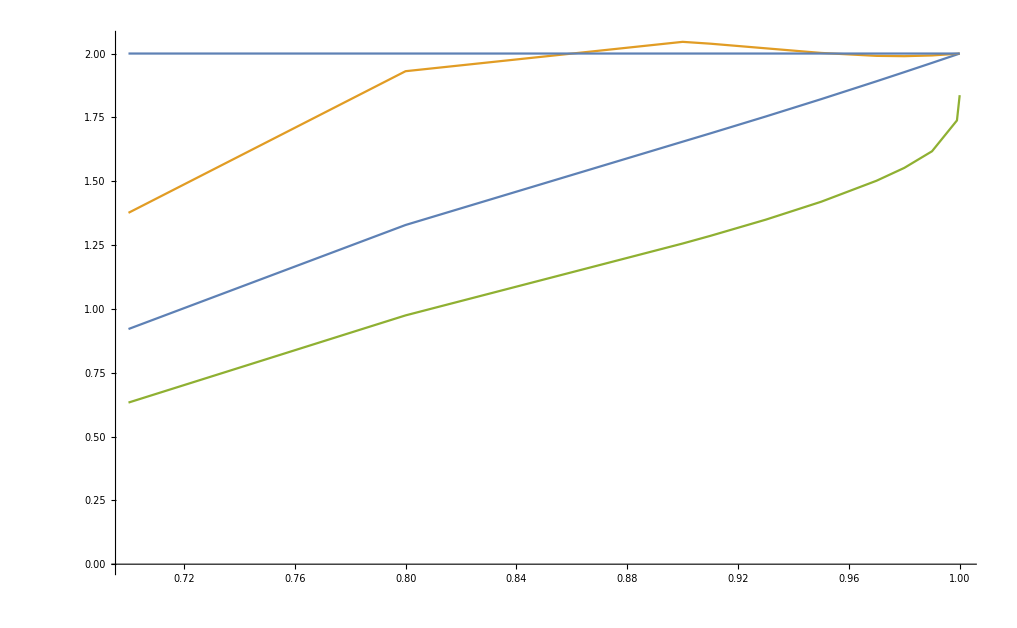

```mathematica
Show[{ListPlot[{a1,a2,a3},Joined->True],Plot[{2},{x,0.7,1},GridLines->{{0.99}}]}]
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

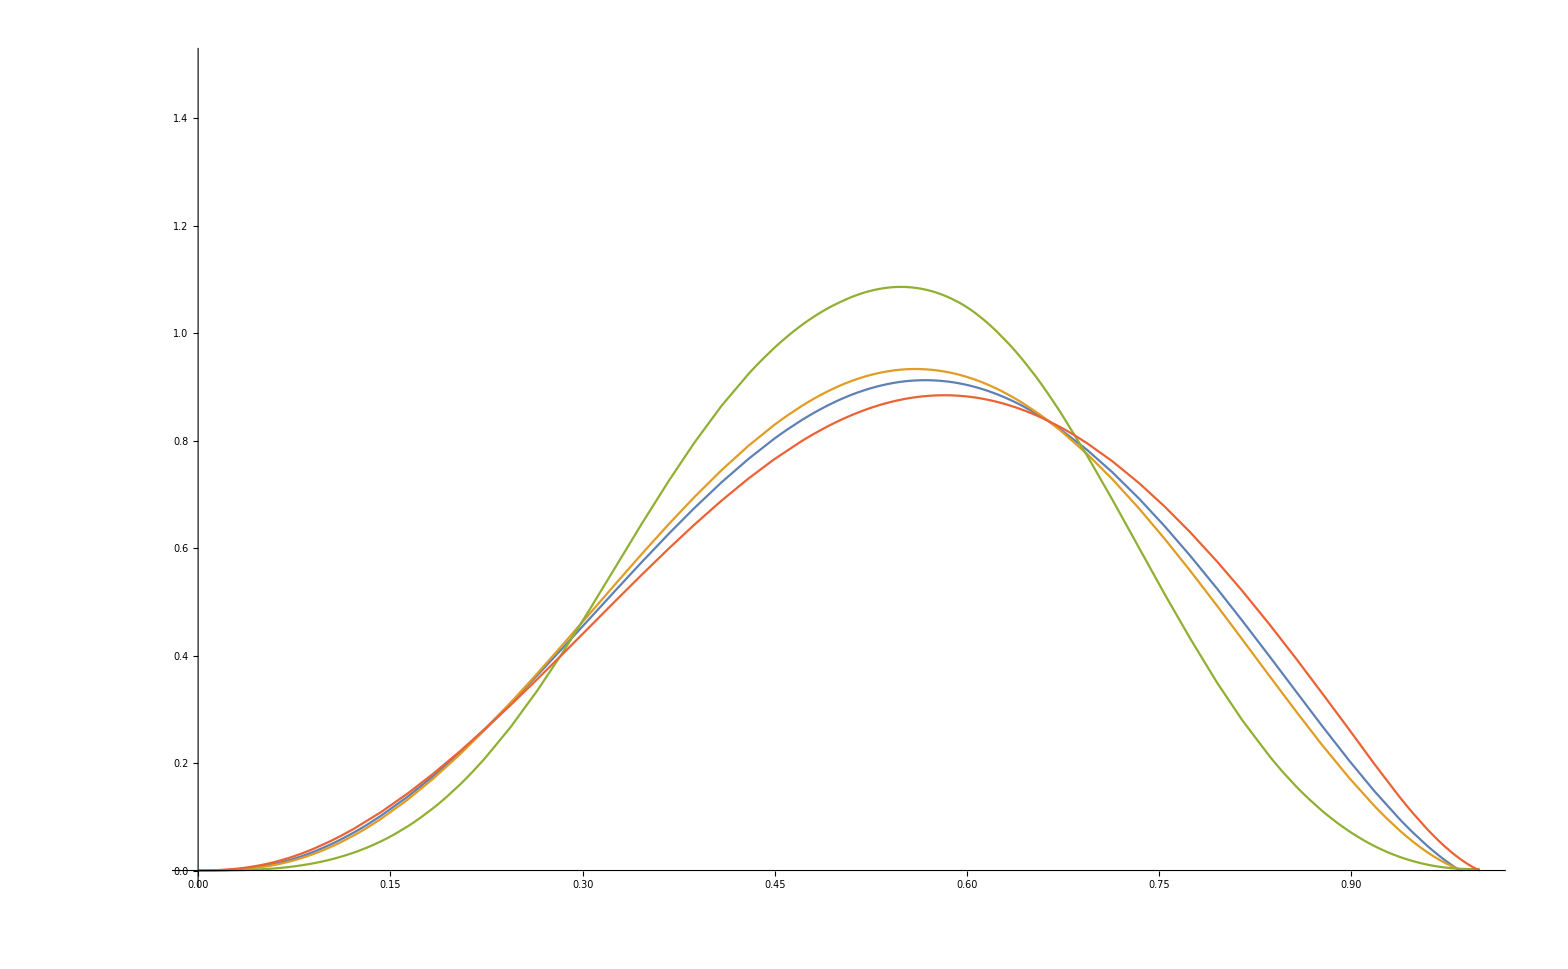

```mathematica
Plot[{tab2[x]*x,tab0[x]*x,tab3[x]*x,tab4[x]*x},{x,0,1},PlotRange->{0,1.5}]
```